```mathematica
<<mf25.m
```

```mathematica
cRaleigh2[α_,β_,ν_]:=Module[{answer,pchhmrA,pchhmrB},
pchhmrA=Pochhammer[α,ν];
pchhmrB=Pochhammer[β,ν];
answer=pchhmrA*pchhmrB/(ν!)^2;
Return[answer]]
```

```mathematica
eRaleigh[α_,β_,ν_]:=Sum[1/(α+p)+1/(β+p)-2/(1+p),{p,0,ν-1}]
```

```mathematica
Fraleigh2[α_,β_,u_,terms_]:=Sum[cRaleigh2[α,β,ν]*u^ν,{ν,0,terms}]
```

```mathematica
FstarRaleigh2[α_,β_,u_,terms_]:=
Module[{ν,fsr},
fsr=Sum[cRaleigh2[α,β,ν]*eRaleigh[α,β,ν]*u^ν,{ν,1,terms}];
Return[fsr]]
```

```mathematica
FstarRaleigh3[n_,m_,x_]:=
Module[{α,β,fsr2},
α = 1/2(1/2-1/m);
 β = 1/2(1/2+1/m);
fsr2=FstarRaleigh2[α,β,x,n];
fsr2=Series[fsr2,{x,0,n}];
Return[fsr2]]
```

```mathematica
Fraleigh4[n_,m_,x_]:=
Module[{α,β,fr2},
α = 1/2(1/2-1/m);
 β = 1/2(1/2+1/m);
fr2=Fraleigh2[α,β,x,n];
fr2=Series[fr2,{x,0,n}];
Return[fr2]]
```

```mathematica
exNo3[n_,m_,J_]:=
Module[{a1,a2,a3,a4},
a1=J*Exp[FstarRaleigh3[n,m,J]/Fraleigh4[n,m,J]];
a2=Series[a1,{J,0,n}];
a3=Collect[Normal[a2],J];
a4=Series[a3,{J,0,n}];
Return[a4]]
```

```mathematica
J[n_,m_]:=1/InverseSeries[exNo3[n,m,x],x]
```

```mathematica
H[n_,m_]:=
Module[{jay,djay,numerator,denominator,answer},
jay=J[n+1,m]; (* n+1 instead of n avoids erros in highest order term. Why? *)
djay=x*D[jay,x];(* x factor by chain rule; x is an exponential fn. *)
numerator=djay^2;
denominator=jay*(jay-1);
answer=Collect[Series[(numerator/denominator)^(1/(m-2)),{x,0,n}],x];
Return[answer]]
```

```mathematica
H4[n_,m_]:=
Module[{jay,djay,numerator,denominator,answer},
jay=J[n+1,m]; (* n+1 instead of n avoids erros in highest order term. Why? *)
djay=x*D[jay,x];(* x factor by chain rule; x is an exponential fn. *)
numerator=djay^2;
denominator=jay*(jay-1);
answer=Collect[Series[(numerator/denominator),{x,0,n}],x];
Return[answer]]
```

```mathematica
deltaDiamond[n_,m_]:=
Module[{answer},
answer=
Collect[Series[H[n+1,m]^3/J[n+1,m],{x,0,n}],x];
Return[answer]]
```

```mathematica
deltaDiamond12[n_,m_]:=
Module[{answer},
answer=
Collect[Series[H4[n+2,m]^3/J[n+2,m],{x,0,n}],x];
Return[answer]]
```

```mathematica
deltaDiamond12Strike[n_,m_]:=
Module[{f},
f=deltaDiamond12[n,m]/.x->(2^6*m^3*x);
c0=Coefficient[f,x,1];
f=Expand[f/c0];
Return[f]]
```

```mathematica
Print[deltaDiamond12Strike[6,3]]
```

x-24 x^2+252 x^3-1472 x^4+4830 x^5-6048 x^6

```mathematica
fi=Collect[deltaDiamond12Strike[25,3],x];
ex=Exponent[fi,x];
no=0;
For[n=0,n<ex,n++;
cf=Coefficient[fi,x,n];
If[cf≠RamanujanTau[n],no++]];
Print[no]
```

0

```mathematica
stream=OpenWrite["run17aug21no61"];
For[m=2,m<153,m++;
fi=deltaDiamond12Strike[50,m];
Write[stream,{m,Collect[fi,x]}]];
Close[stream]
```

run17aug21no61

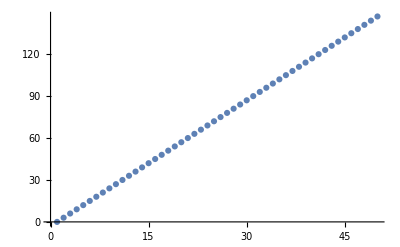

run17aug21no62

```mathematica
stream=OpenRead["run17aug21no61"];
list=ReadList[stream];
Close[stream];
wstream=OpenWrite["run17aug21no62"]; 
degrees={};
For[n=0,n<50,n++;
data={};
For[k=0,k<150,k++;
m=list[[k,1]];
poly=list[[k,2]];
cf=Coefficient[poly,x,n];
AppendTo[data,{m,cf}]
]; (* k *)
ip=InterpolatingPolynomial[data,x];
Write[wstream,{n,ip}];
AppendTo[degrees,{n,Exponent[ip,x]}]
]; (* n *)
Print[ListPlot[degrees]];
Close[wstream]
```

```mathematica
stream=OpenRead["run17aug21no62"];
list=ReadList[stream];
Close[stream];
Print[Length[list]]
```

50

```mathematica
stream=OpenRead["run17aug21no62"];
list=ReadList[stream];
Close[stream];
ntdata={};
For[k=0,k<50,k++;
n=list[[k,1]];
poly=list[[k,2]];
degree=Exponent[poly,x];
fim=factorIntoIrreducibleMonics[poly];
numericalterm=1;
For[j=0,j<Length[fim],j++;
pair=fim[[j]];
base=pair[[1]];
power=pair[[2]];
dg=Exponent[base,x];
If[dg===0,
numericalterm=numericalterm*base^power]];
AppendTo[ntdata,numericalterm-RamanujanTau[n]*(-1)^(n+1)]];
Print[ntdata]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
stream=OpenRead["run17aug21no62"];
list=ReadList[stream];
Close[stream];
no={};
For[k=0,k<50,k++;
n=list[[k,1]];
poly=list[[k,2]];
poly=Collect[poly,x];
divideby=x^(n-1);
pr=PolynomialRemainder[poly,divideby,x];
If[pr!=0,no=AppendTo[no,n]]];
Print[no]
```

{}

```mathematica
stream=OpenRead["run17aug21no62"];
list=ReadList[stream];
Close[stream];
data={};
For[k=2,k<50,k++;
n=list[[k,1]];
poly=list[[k,2]];
divideby=x^(n-1);
poly=PolynomialQuotient[poly,divideby,x];
xp=Exponent[poly,x];
data=AppendTo[data,{n,xp}]];
Print[data]
```

{{3,4},{4,6},{5,8},{6,10},{7,12},{8,14},{9,16},{10,18},{11,20},{12,22},{13,24},{14,26},{15,28},{16,30},{17,32},{18,34},{19,36},{20,38},{21,40},{22,42},{23,44},{24,46},{25,48},{26,50},{27,52},{28,54},{29,56},{30,58},{31,60},{32,62},{33,64},{34,66},{35,68},{36,70},{37,72},{38,74},{39,76},{40,78},{41,80},{42,82},{43,84},{44,86},{45,88},{46,90},{47,92},{48,94},{49,96},{50,98}}

--------------------------------------------------------------

n:  1

-Graphics-

--------------------------------------------------------------

n:  2

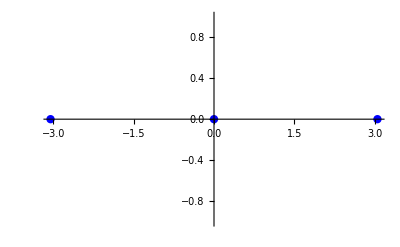

--------------------------------------------------------------

n:  3

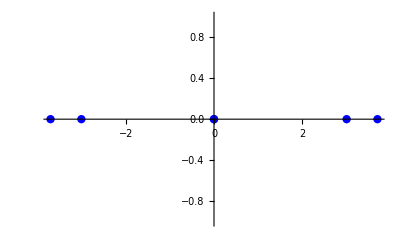

--------------------------------------------------------------

n:  4

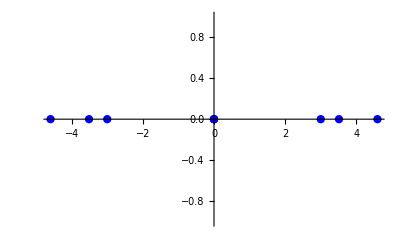

--------------------------------------------------------------

n:  5

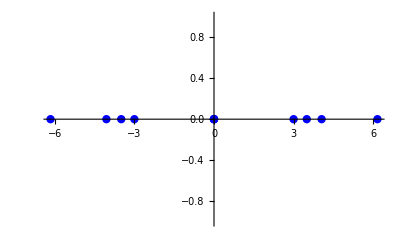

--------------------------------------------------------------

n:  6

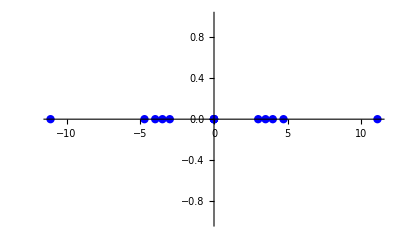

--------------------------------------------------------------

n:  7

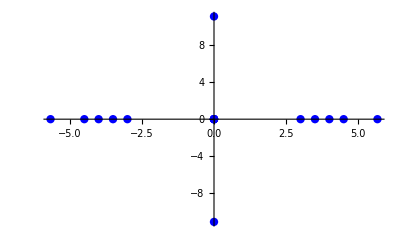

--------------------------------------------------------------

n:  8

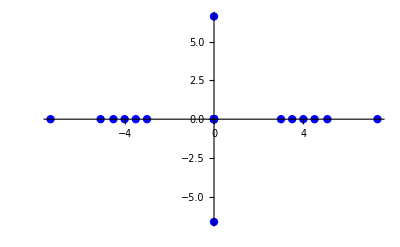

--------------------------------------------------------------

n:  9

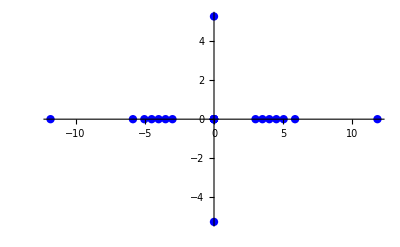

--------------------------------------------------------------

n:  10

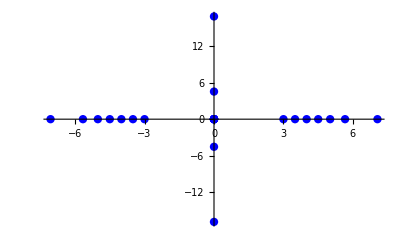

--------------------------------------------------------------

n:  11

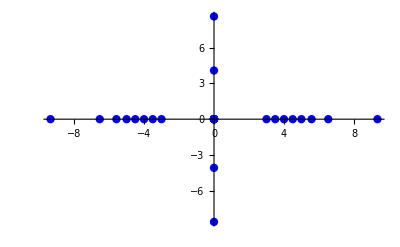

--------------------------------------------------------------

n:  12

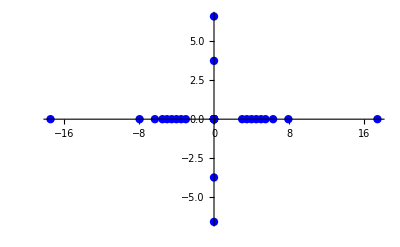

--------------------------------------------------------------

n:  13

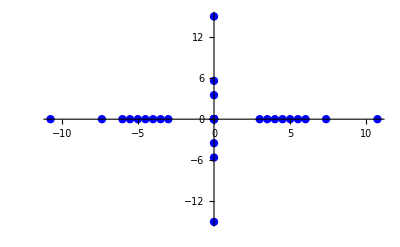

--------------------------------------------------------------

n:  14

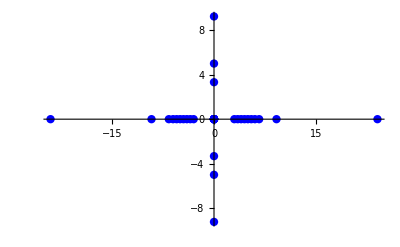

--------------------------------------------------------------

n:  15

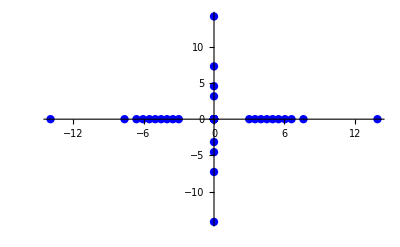

--------------------------------------------------------------

n:  16

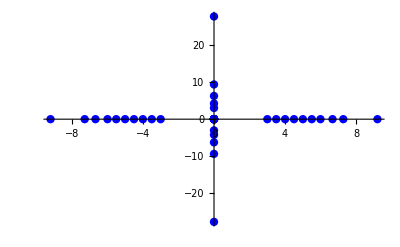

--------------------------------------------------------------

n:  17

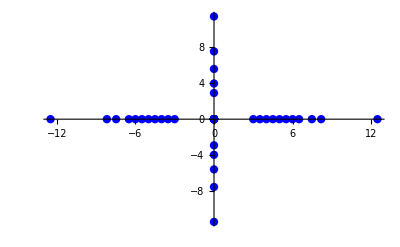

--------------------------------------------------------------

n:  18

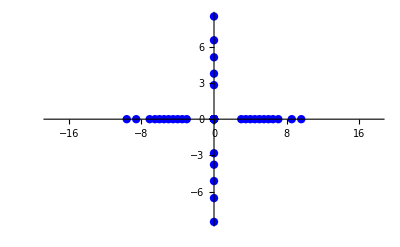

--------------------------------------------------------------

n:  19

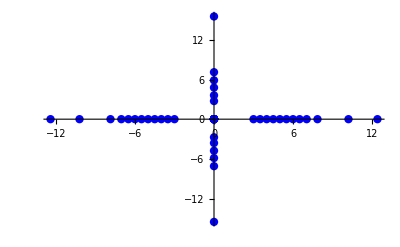

--------------------------------------------------------------

n:  20

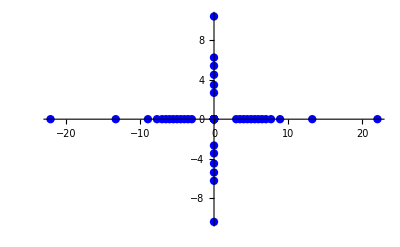

--------------------------------------------------------------

n:  21

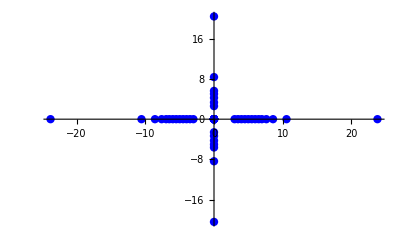

--------------------------------------------------------------

n:  22

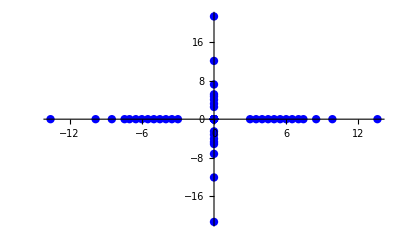

--------------------------------------------------------------

n:  23

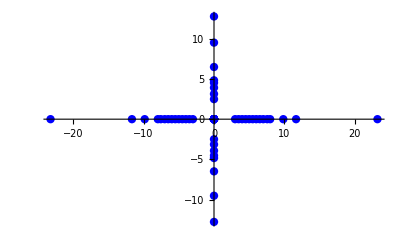

--------------------------------------------------------------

n:  24

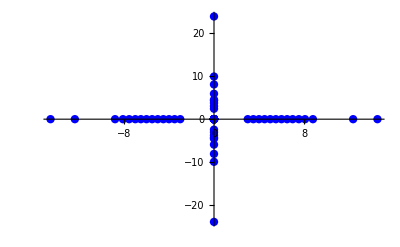

--------------------------------------------------------------

n:  25

$Aborted

mins

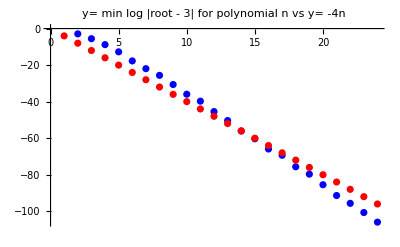

```mathematica
rstream=OpenRead["run17aug21no62"];
list=ReadList[rstream];
Close[rstream];
pointsize=.015;
color=Blue;
mins={};
data={};
degrees={};
no=0;
precision=300;
For[k=0,k<50,k++;
Print["--------------------------------------------------------------"];
n=list[[k,1]];
poly=list[[k,2]];
Print["n:  ",n];
plotRoots2[poly,x,pointsize,color];
roots=listRoots3[poly,x,precision];
If[MemberQ[roots,3]==True,no++];
min=Min[Log[Abs[roots-3]]];
AppendTo[mins,{n,min}];
AppendTo[data,{n,-4*n}]
];
Print["mins"];
lpm=ListPlot[mins,PlotStyle->Blue,PlotLabel->"y= min log |root - 3| for polynomial n vs y= -4n"];
lpd=ListPlot[data,PlotStyle->Red];
Print[Show[lpm,lpd]]
```

--------------------------------------------------------------

n:  1

-Graphics-

--------------------------------------------------------------

n:  2

-Graphics-

--------------------------------------------------------------

n:  3

-Graphics-

--------------------------------------------------------------

n:  4

-Graphics-

--------------------------------------------------------------

n:  5

-Graphics-

--------------------------------------------------------------

n:  6

-Graphics-

--------------------------------------------------------------

n:  7

-Graphics-

--------------------------------------------------------------

n:  8

-Graphics-

--------------------------------------------------------------

n:  9

-Graphics-

--------------------------------------------------------------

n:  10

-Graphics-

--------------------------------------------------------------

n:  11

-Graphics-

--------------------------------------------------------------

n:  12

-Graphics-

--------------------------------------------------------------

n:  13

-Graphics-

--------------------------------------------------------------

n:  14

-Graphics-

--------------------------------------------------------------

n:  15

-Graphics-

--------------------------------------------------------------

n:  16

-Graphics-

--------------------------------------------------------------

n:  17

-Graphics-

--------------------------------------------------------------

n:  18

-Graphics-

--------------------------------------------------------------

n:  19

-Graphics-

--------------------------------------------------------------

n:  20

-Graphics-

--------------------------------------------------------------

n:  21

-Graphics-

--------------------------------------------------------------

n:  22

-Graphics-

--------------------------------------------------------------

n:  23

-Graphics-

--------------------------------------------------------------

n:  24

-Graphics-

--------------------------------------------------------------

n:  25

$Aborted

mins

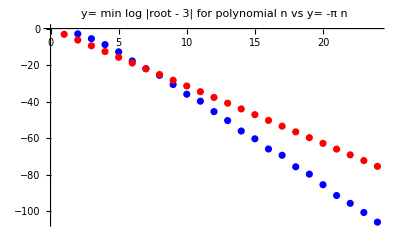

```mathematica
rstream=OpenRead["run17aug21no62"];
list=ReadList[rstream];
Close[rstream];
pointsize=.015;
color=Blue;
mins={};
data={};
degrees={};
no=0;
precision=300;
For[k=0,k<50,k++;
Print["--------------------------------------------------------------"];
n=list[[k,1]];
poly=list[[k,2]];
Print["n:  ",n];
plotRoots2[poly,x,pointsize,color];
roots=listRoots3[poly,x,precision];
If[MemberQ[roots,3]==True,no++];
min=Min[Log[Abs[roots-3]]];
AppendTo[mins,{n,min}];
AppendTo[data,{n,-Pi*n}]
];
Print["mins"];
lpm=ListPlot[mins,PlotStyle->Blue,PlotLabel->"y= min log |root - 3| for polynomial n vs y= -π n"];
lpd=ListPlot[data,PlotStyle->Red];
Print[Show[lpm,lpd]]
```